```mathematica
?LogLogPlot
```

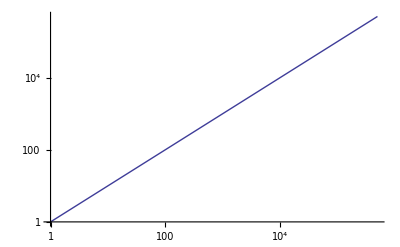

```mathematica
LogLogPlot[x,{x,1,500000}]
```

```mathematica
{First/@airytimes,Range[
```

{21,29,41,67,128,289,752,2150,6473,20004,62591,196981,621538,1963499}

```mathematica
airytimes={{21,0.000142},{29,0.000198},{41,0.000278},{67,0.000434},{128,0.000798},{289,0.001672},{752,0.004206},{2150,0.014066},{6473,0.038119},{20004,0.120574},{62591,0.364217},{196981,1.10596},{621538,3.51858},{1963499,10.8746}};
```

```mathematica
costimes=
{{41,0.001496},{50029,2.40344},{100027,4.78802},{150025,7.12601},{200025,9.35736},{250025,11.766},{300025,14.0633},{350025,16.3969},{400025,18.7202},{450025,21.0496},{500025,23.4105},{550025,25.7219},{600025,28.0574},{650025,30.4243},{700025,32.7308},{750025,35.2572},{800025,38.1089},{850025,39.9069},{900025,44.174},{950025,45.2414},{1000025,47.1681},{1050025,50.1155},{1100025,53.6831},{1150025,56.0851},{1200025,57.3176},{1250025,61.3304},{1300025,63.3431},{1350025,66.5656},{1400025,67.4595},{1450025,70.162},{1500025,73.139},{1550025,74.5608},{1600025,77.6357},{1650025,78.8894},{1700025,81.7603},{1750025,82.1096},{1800025,84.5671},{1850025,86.5941},{1900025,89.1245},{1950025,92.7127},{2000025,95.5456}};
```

```mathematica
smallbandtimes=
{{34,0.000308},{50020,0.426225},{100022,0.811004},{150023,1.24839},{200027,1.64},{250030,1.96937},{300036,2.38099},{350043,2.74828},{400051,3.02962},{450060,3.44419},{500070,3.85062},{550081,4.16286},{600093,4.54145},{650106,4.91765},{700120,5.28947},{750135,5.68505},{800151,6.03972},{850168,6.41845},{900186,6.79781},{950205,7.17231},{1000225,7.54948},{1050246,7.92856},{1100268,8.30277},{1150291,8.72795},{1200315,9.07176},{1250340,9.53101},{1300366,9.82321},{1350393,10.3349},{1400421,10.657},{1450450,11.7952},{1500480,12.2712},{1550511,11.809},{1600543,12.4317},{1650576,13.0229},{1700610,12.8997},{1750645,13.7077},{1800681,13.774},{1850718,13.9679},{1900756,14.6027},{1950795,14.7535},{2000835,15.1189}};
```

```mathematica
Last[airytimes]//#⟦2⟧/#⟦1⟧&
```

5.53838×10^-6

```mathematica
(Last[costimes]//#⟦2⟧/#⟦1⟧&)/7^2
```

9.74943×10^-7

```mathematica
{#⟦1⟧,#⟦2⟧/13^2}&/@costimes
```

{{41,8.85207×10^-6},{50029,0.0142215},{100027,0.0283315},{150025,0.0421657},{200025,0.055369},{250025,0.0696213},{300025,0.0832148},{350025,0.0970231},{400025,0.11077},{450025,0.124554},{500025,0.138524},{550025,0.152201},{600025,0.16602},{650025,0.180025},{700025,0.193673},{750025,0.208622},{800025,0.225496},{850025,0.236136},{900025,0.261385},{950025,0.267701},{1000025,0.279101},{1050025,0.296541},{1100025,0.317651},{1150025,0.331864},{1200025,0.339157},{1250025,0.362902},{1300025,0.374811},{1350025,0.393879},{1400025,0.399169},{1450025,0.41516},{1500025,0.432775},{1550025,0.441188},{1600025,0.459383},{1650025,0.466801},{1700025,0.483789},{1750025,0.485856},{1800025,0.500397},{1850025,0.512391},{1900025,0.527364},{1950025,0.548596},{2000025,0.565359}}

```mathematica
13^2
```

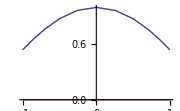

```mathematica
Fun[Cos]
```

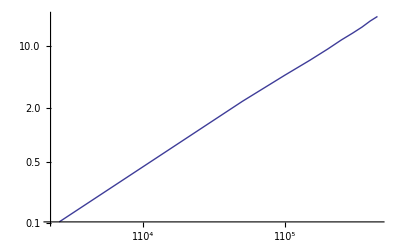

```mathematica
ListLineLogLogPlot[costimes]
```

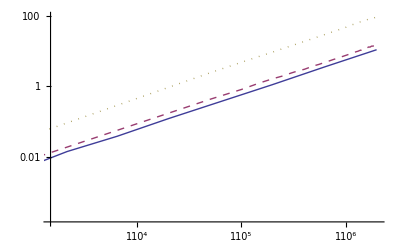

```mathematica
ListLineLogLogPlot[{airytimes,smallbandtimes,costimes},PlotStyle->{{Thick},{Thick,Dashed},{Thick,Dotted}},PlotRange->All]
```

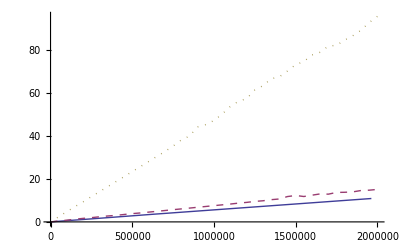

```mathematica
ListLinePlot[{airytimes,smallbandtimes,costimes},PlotStyle->{{Thick},{Thick,Dashed},{Thick,Dotted}},PlotRange->All]
```

```mathematica
.
```

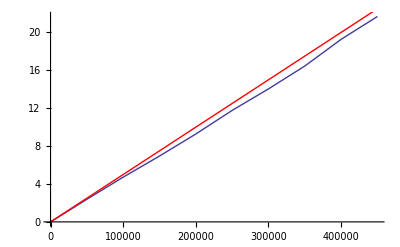

```mathematica
Show[{{41,0.00135},{50029,2.38771},{100027,4.72233},{150025,6.95209},{200025,9.27881},{250025,11.7685},{300025,14.0395},{350025,16.4515},{400025,19.2695},{450025,21.6828}}//ListLinePlot,Plot[.00005x,{x,1,500000},PlotStyle->Red]]
```

```mathematica
e=10^-9
```

1/1000000000

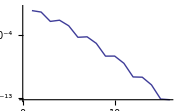

```mathematica
e=1;Fun[AiryAi[(1/e)^(1/3)#]&]//DCTPlot
```

```mathematica
dct=(Fun[AiryAi[(1/e)^(1/3)#]&,UnitInterval,25000]//DCT);
```

```mathematica
$MachineEpsilon
```

2.22045×10^-16

```mathematica
Table[N[AiryAi[-(10^k)^(1/3)],100]//N,{k,11,20}]
```

```mathematica
{-0.027905156151965354,0.02705738360464258,0.044775817580242405,0.01829406779298808,-0.013152978737498166,-0.02249517692130777,0.020321506196299167,-0.0021912611413430574,-0.013261784699976999,0.005242247212492905}
```

```mathematica
{0.13529241631288141,0.027515172874532375,0.00024221691467447962,1.1047532552898686*^-10,1.4576297592861973*^-30,2.994124191362856*^-93,2.6344821520881846*^-291,1.9673821535510539047331462661995204510820943814`15.954589770191005*^-917,3.07027909856258126295695644227318348369105515051418`15.954589770191005*^-2897,9.30693306317955600408639507494421243643901268769907`15.954589770191005*^-9158,4.4833337035423774246553687782693984069358`15.954589770191005*^-28955}
```

```mathematica
k
```

```mathematica
Table[N[AiryAi[-(10^k)^(1/3)],50]//N,{k,0,10}]
```

```mathematica
{0.5355608832923521,0.1271728034584682,0.351913571284756,0.04024123848644319,-0.2607345878897477,-0.19426241417077472,0.1767533932395529,-0.12078802581383595,0.10178242352993307,0.05597189577301992,0.02333382924837296}
```

```mathematica
{0.5355608832923521,0.46826521142593924,0.41015103147749843,0.3808486681201215,0.3670353692081134,0.3606035525476925,0.3576161885387221,0.35622938121523895,0.3555856627976237,0.35528687323241714,0.3551481872073558}
```

```mathematica
dct⟦19990;;20010⟧
```

{-1.50451×10^-15,6.24928×10^-16,3.93427×10^-16,-7.45078×10^-16,2.62758×10^-16,4.73305×10^-16,-6.59002×10^-16,6.03268×10^-17,7.16675×10^-16,-8.82434×10^-16,3.75522×10^-16,1.05199×10^-16,-2.45465×10^-17,-3.49175×10^-16,4.43064×10^-16,-2.47886×10^-16,2.65699×10^-16,-6.56032×10^-16,9.02885×10^-16,-5.02661×10^-16,-3.42969×10^-16}

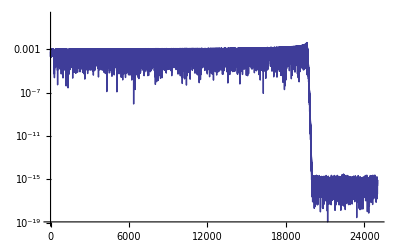

```mathematica
Fun[AiryAi[(1/e)^(1/3)#]&,UnitInterval,25000]//DCTPlot
```

```mathematica
{0.08433236595072038,-0.0344678680495355,-0.08735161277594085,-0.06438982018126162,0.23557885017384145,-0.16616249857716558,-0.015337603605150475,0.09304528921750119,-0.055190132655170254,0.0027123064677967157,0.013813314983905863,-0.007725125532756536,0.0007771221492865396,0.0011056380758533496,-0.0006033048766547295,0.00007456897258777454,0.00005582269639090032,-0.000030236345779994156,4.0771651499431*^-6,1.946501536309077*^-6,-1.0582512737847272*^-6,1.486015480146874*^-7,4.9758892951314027*^-8,-2.737842603323104*^-8,3.9150565740719845*^-9,9.730075356539913*^-10,-5.454969167345558*^-10,7.8485010157614*^-11,1.502568902633783*^-11,-8.635217541019813*^-12,1.2431861096118269*^-12,2.0372245557176427*^-13,-1.1121659149182506*^-13}
```

```mathematica
{0.23984898363059512,-0.16113751645189198,-0.14413194016224,0.1203966893882936,-0.02348904387198854,-0.00836821171008774,0.0053022556990206466,-0.0008125046605158492,-0.00017483112220273488,0.00009470810867189076,-0.000012336092373853307,-1.880389559952571*^-6,9.129629307658291*^-7,-1.050223924292402*^-7,-1.2327742770507455*^-8,5.502033054951644*^-9,-5.720031856764034*^-10,-5.442159788453524*^-11,2.268379092944998*^-11,-2.1650814783512677*^-12,-1.7882312503872916*^-13,6.801051936616897*^-14}
```

```mathematica
N[AiryAi[-(1/e)^(1/3)],50]//N
```

0.351914

```mathematica
0.351913571284756
```

```mathematica
0.00024221691467447962
```

```mathematica
0.027515172874532375
```

```mathematica
0.1271728034584682
```

```mathematica
0.05597189577301992
```